DEVBIO 232 Homework 1
January 31st, 2019
Samuel Morabito

#### Problem 1: Simple Production Destruction Model

```mathematica
(* reset button for all variables *)
ClearAll["Global`*"]
```

Problem 1b:

```mathematica
system= {
A'[t] == p-r A[t], A[0]==Azero
};

(* getting the exact symbolic solution *)
sol1 = DSolve[system,A[t],t]
```

{{A[t]→(ⅇ^(-r t) (-p+ⅇ^(r t) p+Azero r))/r}}

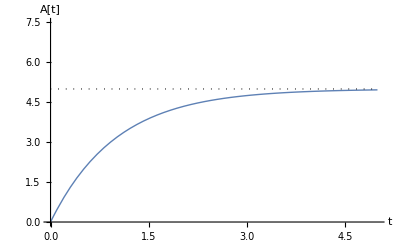

```mathematica
(* plot the solution *)
parameters1 = {p-> 5, Azero-> 0, r->1};
case1 = sol1 /.parameters1;

p1 = Plot[{A[t]/.case1},{t,0,5},PlotStyle->Thick,PlotRange->{0,7.5},AxesLabel->{"t","A[t]"}];
l1 = Graphics[{Dotted, Line[{{0,5},{5,5}}]}];
Show[p1,l1]
```

#### Problem 1c:

```mathematica
Manipulate[
parameters2= {p->pValue,Azero-> 0, r-> rValue};
Plot[{A[t]/.sol1/.parameters2},{t,0,20},PlotStyle->Thick,PlotRange->{-0.2,10},AxesLabel->{"t","A[t]"}],
{pValue,0.2,10}, {rValue, 0.2,10}
]
```

#### Problem 2: Simple Transport Model

```mathematica
system2= {
mb'[t] == -Subscript[k, 1] mb[t], mb[0]== mbzero,
cy'[t] == Subscript[k, 1] mb[t] - Subscript[k, 2] cy[t], cy[0] == 0,
nu'[t] == Subscript[k, 2] cy[t], nu[0] == 0
};

(* getting the exact symbolic solution *)
sol2 = DSolve[system2,{mb[t], cy[t], nu[t]}, t]
```

{{cy[t]→-(ⅇ^(-t k_1-t k_2) (-ⅇ^(t k_1)+ⅇ^(t k_2)) mbzero k_1)/(k_1-k_2),mb[t]→ⅇ^(-t k_1) mbzero,nu[t]→(ⅇ^(-t k_1-t k_2) mbzero (-ⅇ^(t k_1) k_1+ⅇ^(t k_1+t k_2) k_1+ⅇ^(t k_2) k_2-ⅇ^(t k_1+t k_2) k_2))/(k_1-k_2)}}

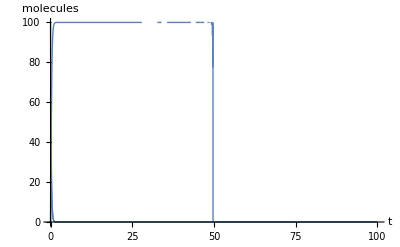

```mathematica
(* plot the solution *)
parameters2 = {Subscript[k, 1]-> 5, Subscript[k, 2]-> 10, mbzero-> 100};
case2 = sol2 /.parameters2;

p1 = Plot[{mb[t]/.case2},{t,0,100},PlotStyle->Thick,PlotRange->{0,100},AxesLabel->{"t","molecules"}];
p2 = Plot[{cy[t]/.case2},{t,0,100},PlotStyle->Thick,PlotRange->{0,100},AxesLabel->{"t","molecules"}];
p3 = Plot[{nu[t]/.case2},{t,0,100},PlotStyle->Thick,PlotRange->{0,100},AxesLabel->{"t","molecules"}];
Show[p1,p2,p3]
```